

```mathematica
Plot[x,{x,-2,2}]
```

```mathematica
Sunrise[]
```

Minute: Sun 15 Sep 2019 06:38GMT-7.

```mathematica
Sunset[]
```

Minute: Sun 15 Sep 2019 19:02GMT-7.

```mathematica
DaylightQ[]
```

False

```mathematica
DayHemisphere[]
```

DayHemisphere[]

```mathematica
SunPosition[]
```

{343.64 °,-50.29 °}

```mathematica
Solve[n (G Subscript[m, 1] Subscript[m, 2])/r^2== (G Subscript[m, 1] Subscript[m, 2])/(r+k)^2,k,Reals]
```

{{k→ConditionalExpression[-r-√(r^2/n),n>0]},{k→ConditionalExpression[-r+√(r^2/n),n>0]}}

```mathematica
FullSimplify[Solve[n (G Subscript[m, 1] Subscript[m, 2])/r^2== (G Subscript[m, 1] Subscript[m, 2])/(r+k)^2,k,Reals],k∈Reals∧n∈]
```

{{k→-r-√(r^2/n)},{k→-r+√(r^2/n)}}

```mathematica
√(r^2/n)-x
```

√(r^2/n)-x

```mathematica
√(r^2/n)-r
```

-r+√(r^2/n)

```mathematica
Manipulate[Plot[-r+√(r^2/n),{r,-8,8}],{n,-8,8}]
```

```mathematica
Manipulate[Plot[-r+√(r^2/n),{r,-8,8}],{n,1,20,1}]
```

```mathematica
Manipulate[
Plot[-r+√(r^2/n),{r,-8,8},AxesLabel->{r,k}]
,{n,1,20,1}]
```

```mathematica
PlanetData["Earth"]
```

Earth

```mathematica
NBodySimulation["InverseSquare",{<|"Mass"->1,"Position"->{-1/3},"Velocity"->{0}|>,
<|"Mass"->2,"Position"->{1/3},"Velocity"->{0}|>},10]
```

NBodySimulationData[2, <0.349066>]

```mathematica
Plot[Evaluate[Out[15][All,"Position",t]],{t,0,10}]
```

-Graphics-

```mathematica
NBodySimulation["InverseSquare",{<|"Mass"->1,"Position"->{0,0},"Velocity"->{0,.5}|>,
<|"Mass"->1,"Position"->{1,1},"Velocity"->{0,-.5}|>,
<|"Mass"->1,"Position"->{0,1},"Velocity"->{0,0}|>},4]
```

NBodySimulationData[3, <4.>]

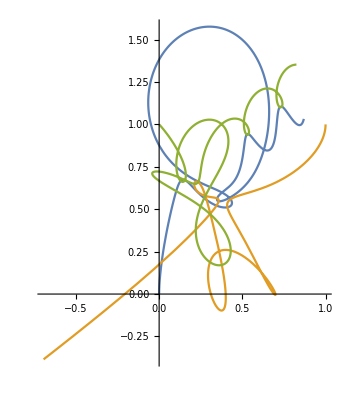

```mathematica
ParametricPlot[Evaluate[Out[17][All,"Position",t]],{t,0,4}]
```

```mathematica
Manipulate[
ParametricPlot[Evaluate[Out[17][All,"Position",t]],{t,0,a}]
,{a,0.001,4}]
```

```mathematica
Manipulate[
ParametricPlot[
Evaluate[Out[17][All,"Position",t]]
,{t,0,a}
,PlotRange->{{-2,2},{-2,2}}]
,{a,0.001,4}]
```

```mathematica
Manipulate[
ParametricPlot[
Evaluate[Out[17][All,"Position",t]]
,{t,0,a}
,PlotRange->{{-2,2},{-2,2}},ImageSize->Large]
,{a,0.001,4}]
```

```mathematica
NBodySimulation["InverseSquare",{<|"Mass"->1,"Position"->{-1,0},"Velocity"->{0,-1}|>,
<|"Mass"->1,"Position"->{1,0},"Velocity"->{0,1}|>},10]
```

NBodySimulationData[…]

```mathematica
Manipulate[
ParametricPlot[
Evaluate[Out[22][All,"Position",t]]
,{t,0,a}
,PlotRange->{{-2,2},{-2,2}},ImageSize->Large]
,{a,0.001,10}]
```

```mathematica
Manipulate[
ParametricPlot[
Evaluate[
NBodySimulation["InverseSquare",{
<|"Mass"->10,"Position"->{-1,0},"Velocity"->{0,-1}|>,
<|"Mass"->10,"Position"->{1,0},"Velocity"->{0,1}|>
},10][All,"Position",t]
]
,{t,0,a}
,PlotRange->{{-2,2},{-2,2}},ImageSize->Large]
,{a,0.001,10}]
```

```mathematica
With[{mass=5},
Manipulate[
ParametricPlot[
Evaluate[
NBodySimulation["InverseSquare",{
<|"Mass"->mass,"Position"->{-1,0},"Velocity"->{0,-1}|>,
<|"Mass"->mass,"Position"->{1,0},"Velocity"->{0,1}|>
},10][All,"Position",t]
]
,{t,0,a}
,PlotRange->{{-2,2},{-2,2}},ImageSize->Large]
,{a,0.001,10}]
]
```

```mathematica
Manipulate[
ParametricPlot[
Evaluate[
NBodySimulation["InverseSquare",{
<|"Mass"->a,"Position"->{-1,0},"Velocity"->{0,-1}|>,
<|"Mass"->a,"Position"->{1,0},"Velocity"->{0,1}|>
},10][All,"Position",t]
]
,{t,0,10}
,PlotRange->{{-2,2},{-2,2}},ImageSize->Large]
,{a,1,10,1}]
```

```mathematica
Manipulate[
ParametricPlot[
Evaluate[
NBodySimulation["InverseSquare",{
<|"Mass"->a,"Position"->{-1,0},"Velocity"->{0,-1}|>,
<|"Mass"->a,"Position"->{1,0},"Velocity"->{0,1}|>
},10][All,"Position",t]
]
,{t,0,10}
,PlotRange->{{-2,2},{-2,2}},ImageSize->Large]
,{a,1,10}]
```

```mathematica
With[{mass=4},
Manipulate[
ParametricPlot[
Evaluate[
NBodySimulation["InverseSquare",{
<|"Mass"->mass,"Position"->{-1,0},"Velocity"->{0,-1}|>,
<|"Mass"->mass,"Position"->{1,0},"Velocity"->{0,1}|>
},10][All,"Position",t]
]
,{t,0,a}
,PlotRange->{{-2,2},{-2,2}},ImageSize->Large]
,{a,0.001,10}]
]
```

```mathematica
{1,1} .{a,b}=={1,0}
```

a+b=={1,0}

```mathematica
∇.{x,x}
```

```mathematica
3+5
```

8

```mathematica
Div[{x,x},x]
```

{x,x}x

```mathematica
{x,x}.RotationMatrix[θ]
```

{x Cos[θ]+x Sin[θ],x Cos[θ]-x Sin[θ]}

```mathematica
FullSimplify[{x,x}.(Normalize[{x,x}.RotationMatrix[θ]]),{x,θ}∈Reals]
```

√2 Abs[x] Cos[θ]

```mathematica
Manipulate[Plot[√2 Abs[x] Cos[θ],{x,-5.116672736016927,5.116672736016927}],{θ,-3.802580299163373,3.802580299163373}]
```

```mathematica
Plot3D[√2 Abs[x] Cos[θ],{x,0,1},{θ,0,2π}]
```

-Graphics3D-

```mathematica
Plot3D[√2 Abs[x] Cos[θ],{x,0,1},{θ,0,2π},PlotLegends->"Expressions",ImageSize->Large,PlotTheme->"Business",AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[√2 Abs[x] Cos[θ],{x,0,1},{θ,0,2π},PlotLegends->"Expressions",ImageSize->Large,PlotTheme->"Business",AxesLabel->Automatic,Mesh->Full]
```

-Graphics3D-

```mathematica
FullSimplify[{x,x^2}.(Normalize[{x,x^2}.RotationMatrix[θ]]),{x,θ}∈Reals]
```

√(1+x^2) Abs[x] Cos[θ]

```mathematica
Manipulate[Plot[√(1+x^2) Abs[x] Cos[θ],{x,-1.9250905282611437,1.9250905282611437}],{θ,-6.283185307179586,6.283185307179586}]
```

```mathematica
Plot3D[√2 Abs[x] Cos[θ]
,{x,0,1},{θ,0,2π}
,PlotLegends->"Expressions",ImageSize->Large,PlotTheme->"Business",AxesLabel->Automatic,Mesh->Full
]
```

-Graphics3D-

```mathematica
Plot3D[√2 Abs[x] Cos[θ]
,{x,-3,3},{θ,0,2π}
,PlotLegends->"Expressions",ImageSize->Large,PlotTheme->"Business",AxesLabel->Automatic,Mesh->Full
]
```

-Graphics3D-

```mathematica
Plot3D[√2 Abs[x] Cos[θ]
,{x,-10,10},{θ,0,2π}
,PlotLegends->"Expressions",ImageSize->Large,PlotTheme->"Business",AxesLabel->Automatic,Mesh->Full
]
```

-Graphics3D-

```mathematica
ArcTan[1]
```

π/4

```mathematica
ArcTan[0]
```

0

```mathematica
ArcTan[-1]
```

-π/4

```mathematica
ArcTan[x]
```

ArcTan[x]

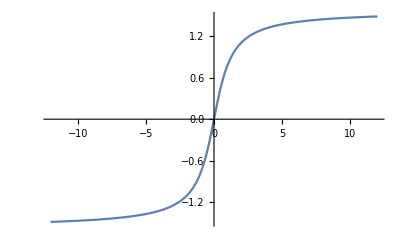

```mathematica
Plot[ArcTan[x],{x,-12.,12.}]
```

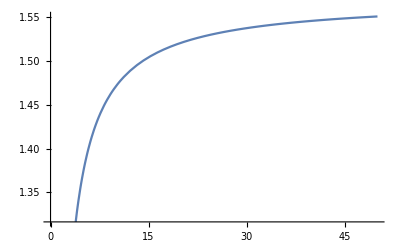

```mathematica
Plot[ArcTan[x],{x,0,50}]
```

```mathematica
Limit[ArcTan[x],x->∞]
```

π/2

```mathematica
π-π/2
```

π/2

```mathematica
√(1+x^2) Abs[x] Cos[θ]
```

√(1+x^2) Abs[x] Cos[θ]

```mathematica
FullSimplify[{x,f[x]}.(Normalize[{x,f[x]}.RotationMatrix[θ]]),{x,f[x],θ}∈Reals]
```

Cos[θ] √(x^2+f[x]^2)

```mathematica
FullSimplify[{x,f'[x]}.(Normalize[{1,f'[0]}.RotationMatrix[θ]]),{x,f[x],f'[x],θ}∈Reals]
```

(x (Cos[θ]+Sin[θ] f'[0])+(-Sin[θ]+Cos[θ] f'[0]) f'[x])/(√(1+Abs[f'[0]]^2))

```mathematica
FullSimplify[{x,1}.(Normalize[{1,1}.RotationMatrix[θ]]),{x,f[x],f'[x],θ}∈Reals]
```

((1+x) Cos[θ]+(-1+x) Sin[θ])/(√2)

```mathematica
Manipulate[Plot[((1+x) Cos[θ]+(-1+x) Sin[θ])/(√2),{x,-4.400754570127704,4.400754570127704}],{θ,-4.600996821166785,4.600996821166785}]
```

```mathematica
Plot3D[
((1+x) Cos[θ]+(-1+x) Sin[θ])/(√2)
,{x,-10,10},{θ,0,2π}
,PlotLegends->"Expressions",ImageSize->Large,PlotTheme->"Business",AxesLabel->Automatic,Mesh->Full
]
```

-Graphics3D-

```mathematica
((1+x) Cos[θ]+(-1+x) Sin[θ])/(√2)/.θ->0==((1+x) Cos[θ]+(-1+x) Sin[θ])/(√2)/.θ->2π
```

((1+x) Cos[0==(1+x)/(√2)]+(-1+x) Sin[0==(1+x)/(√2)])/(√2)

```mathematica
(((1+x) Cos[θ]+(-1+x) Sin[θ])/(√2)/.θ->0)==(((1+x) Cos[θ]+(-1+x) Sin[θ])/(√2)/.θ->2π)
```

True

```mathematica
FullSimplify[{1,f'[x]}.(Normalize[Normalize[{1,f'[0]}].Normalize[RotationMatrix[θ]]]),{x,f[x],f'[x],θ}∈Reals]
```

{1,f'[x]}.Normalize[{1/(√(1+Abs[f'[0]]^2)),f'[0]/(√(1+Abs[f'[0]]^2))}.Normalize[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]]

```mathematica
FullSimplify[Normalize[{1,f'[x]}].(Normalize[Normalize[{1,f'[0]}].Normalize[RotationMatrix[θ]]]),{x,f[x],f'[x],θ}∈Reals]
```

{1/(√(1+f'[x]^2)),f'[x]/(√(1+f'[x]^2))}.Normalize[{1/(√(1+Abs[f'[0]]^2)),f'[0]/(√(1+Abs[f'[0]]^2))}.Normalize[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]]

```mathematica
With[{f=Identity},
FullSimplify[
Normalize[{1,f'[x]}].(Normalize[Normalize[{1,f'[0]}].Normalize[RotationMatrix[θ]]])
,{x,f[x],f'[x],θ}∈Reals
]
]
```

{1/(√2),1/(√2)}.Normalize[{1/(√2),1/(√2)}.Normalize[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]]

```mathematica
With[{f=Identity},
FullSimplify[
Normalize[{1,f'[x]}].
(Normalize[Normalize[{1,f'[0]}].RotationMatrix[θ]])
,{x,f[x],f'[x],θ}∈Reals
]
]
```

Cos[θ]

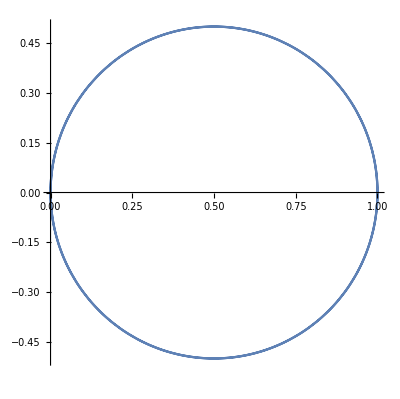

```mathematica
PolarPlot[Cos[θ],{θ,0,2 π}]
```

```mathematica
With[{f=Function[x,x^2]},
FullSimplify[
Normalize[{1,f'[x]}].
(Normalize[Normalize[{1,f'[0]}].RotationMatrix[θ]])
,{x,f[x],f'[x],θ}∈Reals
]
]
```

(Cos[θ]-2 x Sin[θ])/(√(1+4 x^2))

```mathematica
Manipulate[Plot[(Cos[θ]-2 x Sin[θ])/(√(1+4 x^2)),{x,-4.316312667089884,4.203034473009707}],{θ,-3.9821742170089243,3.8683827385310536}]
```

```mathematica
Plot3D[
(Cos[θ]-2 x Sin[θ])/(√(1+4 x^2))
,{x,-10,10},{θ,0,2π}
,PlotLegends->"Expressions",ImageSize->Large,PlotTheme->"Business",AxesLabel->Automatic,Mesh->Full
]
```

-Graphics3D-

```mathematica
D[(Cos[θ]-2 x Sin[θ])/(√(1+4 x^2)),θ]
```

(-2 x Cos[θ]-Sin[θ])/(√(1+4 x^2))

```mathematica
Plot3D[
(-2 x Cos[θ]-Sin[θ])/(√(1+4 x^2))
,{x,-10,10},{θ,0,2π}
,PlotLegends->"Expressions",ImageSize->Large,PlotTheme->"Business",AxesLabel->Automatic,Mesh->Full
]
```

-Graphics3D-

```mathematica
Binom
```

Binom

```mathematica
BinomialDistribution[0,1]
```

BinomialDistribution[0,1]

```mathematica
PDF[BinomialDistribution[0,1],x]
```

Piecewise[{{1, x==0}, {0, True}}]

```mathematica
BinormalDistribution[0,1]
```

BinormalDistribution[0,1]

```mathematica
BinormalDistribution[{0,0},1]
```

BinormalDistribution[{0,0},1]

```mathematica
BinormalDistribution[{0,0},1]
```

BinormalDistribution[{0,0},1]

```mathematica
RandomVariate[BinormalDistribution[{1,2},{1.5,2},0.6],10^4]
```

{{0.22047,0.0499185},{2.67842,2.74908},{3.5001,3.44758},{2.04017,2.85924},{1.58717,-1.33121},9990,{0.864306,2.08903},{1.64403,1.97565},{1.45538,2.75931},{2.9473,4.12432},{0.591269,0.402354}}
 |  |  |  |

```mathematica
{Histogram3D[Out[75],30,"PDF",ColorFunction->"Rainbow",PlotRange->{{-5,6},{-3,7},All}],Plot3D[PDF[𝒹,{x,y}],{x,-5,6},{y,-3,7},ColorFunction->"Rainbow",PlotPoints->35,PlotRange->All]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
BinormalDistribution[{0,0},{1,1}]
```

BinormalDistribution[{0,0},{1,1}]

```mathematica
BinormalDistribution[{0,1}]
```

BinormalDistribution[{0,1}]

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
RevolutionPlot3D[(ⅇ^(-x^2/2))/(√(2 π)),{x,-1,1}]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[(ⅇ^(-x^2/2))/(√(2 π)),{x,-3,3}]
```

-Graphics3D-

```mathematica
(ⅇ^(-(x+y)^2/2))/(√(2 π))
```

(ⅇ^(-1/2 (x+y)^2))/(√(2 π))

```mathematica
Plot3D[(ⅇ^(-1/2 (x+y)^2))/(√(2 π)),{x,-5.013116544267941,5.013116544267941},{y,-5.013116544267941,5.013116544267941}]
```

-Graphics3D-

```mathematica
(ⅇ^(-(x^2+y^2)/2))/(√(2 π))
```

(ⅇ^(1/2 (-x^2-y^2)))/(√(2 π))

```mathematica
Plot3D[(ⅇ^(1/2 (-x^2-y^2)))/(√(2 π)),{x,-0.5485147527566367,0.5485147527566367},{y,-0.5485147527566367,0.5485147527566367}]
```

-Graphics3D-

```mathematica
Plot3D[(ⅇ^(1/2 (-x^2-y^2)))/(√(2 π)),{x,y}∈Disk[{0,0},5]]
```

-Graphics3D-

```mathematica
Plot3D[(ⅇ^(1/2 (-x^2-y^2)))/(√(2 π)),{x,y}∈Disk[{0,0},5],ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

```mathematica
Show[{
Plot3D[(ⅇ^(1/2 (-x^2-y^2)))/(√(2 π)),{x,y}∈Disk[{0,0},5],ImageSize->Large,PlotRange->Full],
ParametricPlot3D[{t,t,(ⅇ^(1/2 (-t^2-t^2)))/(√(2 π))},{t,-5,5}]
}]
```

-Graphics3D-

```mathematica
With[{tx=Identity,ty=Identity},
Show[{
Plot3D[(ⅇ^(1/2 (-x^2-y^2)))/(√(2 π)),{x,y}∈Disk[{0,0},5],ImageSize->Large,PlotRange->Full],
ParametricPlot3D[{tx[t],ty[t],(ⅇ^(1/2 (-tx[t]^2-ty[t]^2)))/(√(2 π))},{t,-5,5}]
}]
]
```

-Graphics3D-

```mathematica
With[{tx=Function[t,t-1],ty=Identity},
Show[{
Plot3D[(ⅇ^(1/2 (-x^2-y^2)))/(√(2 π)),{x,y}∈Disk[{0,0},5],ImageSize->Large,PlotRange->Full],
ParametricPlot3D[{tx[t],ty[t],(ⅇ^(1/2 (-tx[t]^2-ty[t]^2)))/(√(2 π))},{t,-5,5}]
}]
]
```

-Graphics3D-

```mathematica
ComplexPlot[Tan[z],{z,-5-5I,5+5I}]
```

-Graphics-

```mathematica
ComplexPlot3D[Tan[z],{z,-5-5I,5+5I}]
```

-Graphics3D-

```mathematica
ComplexPlot[Gamma[z],{z,-5-5I,5+5I}]
```

-Graphics-

```mathematica
ComplexPlot3D[Gamma[z],{z,-5-5I,5+5I}]
```

-Graphics3D-